Model from the 2003 paper “EFFECTS OF FIRE AND HERBIVORY ON THE STABILITY OF SAVANNA ECOSYSTEMS”
Scenario C: high water influx, water_in=750

Define parameters:

```mathematica
u=0.6;
rh=1.0;
rw=0.5;
dh=0.9;dw=0.4;
alpha=0.4;
beta=300;
p=1;
kh=0.1;
kw=0.01;
n=0.1;
a=0.5;
```

Define water recharge rates:

```mathematica
win=750;
ws=alpha*(win-beta);

wt= win-ws;
```

Define system without fire effects

```mathematica
dhdt[H_,W_]:=rh*wt*(H)/(H+u*W+p*ws)-dh*H
```

```mathematica
dwdt[H_,W_]:=rw*(wt*(u*W)/(H+u*W+p*ws)+ws)-dw*W
```

```mathematica
p3=Plot3D[dhdt[H,W],{H,0,400},{W,0,400},PlotStyle->Blue];
p4=Plot3D[dwdt[H,W],{H,0,400},{W,0,400}];
Show[p3,p4]
```

-Graphics3D-

Find Fixed points

```mathematica
Simplify[Solve[dhdt[H,W]==0,H]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.},{H→453.333-0.6 W}}

```mathematica
Simplify[Solve[H==453.3333333333333-0.6* W,W]]
```

{{W→755.556-1.66667 H}}

```mathematica
p1=Plot[755.5555555555555-1.6666666666666667*H,{H,0,300}];
```

```mathematica
Simplify[Solve[dwdt[H,W]==0,W]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{W→318.75-0.833333 H-0.416667 √(974025.-900. H+4. H^2)},{W→0.416667 (765.-2. H+√(974025.-900. H+4. H^2))}}

```mathematica
p2=Plot[0.4166666666666667*(765-2*H+√(974025-900* H+4* H^2)),{H,0,300},PlotStyle->Red];
p5=Plot[318.75-0.8333333333333334*H-0.4166666666666667* √(974025-900* H+4* H^2),{H,0,300},PlotStyle->Red];
```

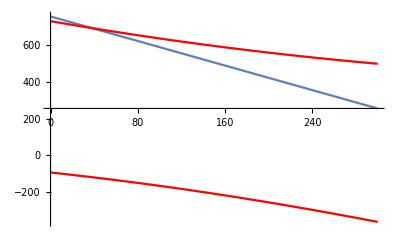

```mathematica
Show[p1,p2,p5,PlotRange->Full]
```

```mathematica
fp=Simplify[Solve[dwdt[H,W]==0 && dhdt[H,W]==0,{H,W}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.,W→-92.4696},{H→37.9487,W→692.308},{H→0.,W→729.97}}

```mathematica
fp1=Part[fp,1]
```

{H→0.,W→-92.4696}

```mathematica
fp2=Part[fp,2]
```

{H→37.9487,W→692.308}

Partial Derivatives evaluated at first fixed point: unstable

```mathematica
j11=D[dhdt[H,W],H]/.fp1
```

3.67764

```mathematica
j12=D[dhdt[H,W],W]/.fp1
```

0.

```mathematica
j21=D[dwdt[H,W],H]/.fp1
```

1.01983

```mathematica
j22=D[dhdt[H,W],W]/.fp1
```

0.

```mathematica
J={{j11,j12},{j21,j22}}
Eigenvalues[J]
Eigenvectors[J]
```

{{3.67764,0.},{1.01983,0.}}

{3.67764,0.}

{{0.963635,0.267222},{0.,1.}}

Partial Derivatives evaluated at second fixed point: attracting

```mathematica
j11=D[dhdt[H,W],H]/.fp2
```

-0.9

```mathematica
j12=D[dhdt[H,W],W]/.fp2
```

-0.54

```mathematica
j21=D[dwdt[H,W],H]/.fp2
```

3.05628×10^-17

```mathematica
j22=D[dhdt[H,W],W]/.fp2
```

-0.54

```mathematica
J={{j11,j12},{j21,j22}}
Eigenvalues[J]
Eigenvectors[J]
```

{{-0.9,-0.54},{3.05628×10^-17,-0.54}}

{-0.9,-0.54}

{{1.,0.},{-0.83205,0.5547}}